-Graphics3D-

-Graphics3D-

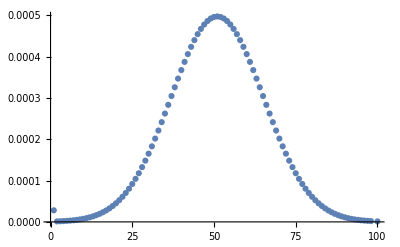

```mathematica
ClearAll["Global`*"]
ClearSystemCache[]

(*field transport*)
n=100;
config={};
c={};
nextconfig= ConstantArray[0,{100,100}]; 

(*constant velocities of movement*)
wx=-.01;
wy= .03;

(*modulo functions correcting for index*)
Xp[x_,n_]:=If[Mod[x+1,n]==0,1,Mod[x+1,n]];
Xs[x_,n_]:=If[Mod[x-1,n]==0,1,Mod[x-1,n]];
Yp[y_,n_]:=If[Mod[y+1,n]==0,1,Mod[y+1,n]];
Ys[y_,n_]:=If[Mod[y-1,n]==0,1,Mod[y+1,n]];

(*instantiates x and y vectors as xvs and yvs*)
meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]};
{xvs,yvs}=meshgrid[Range[0,.99,.01],Range[0,.99,.01]];

(*global vars can be passed by reference*)
Attributes[initialize]=HoldFirst;
Attributes[observe]=HoldFirst;
Attributes[update]=HoldFirst;

(*defines function field equation*)
initialize[]:=
	Module[{},config=Exp[-((xvs-0.5)^2+(yvs-0.5)^2)/(0.2^2)];c=config;];

(*assigns xvs, yvs and config to a table of 100 3x1 vectors and then plots the table*)
observe[]:=Module[{},table=Transpose@{#&@@@xvs,#&@@@yvs,#&@@@config};Print[ListPlot3D[config-c,DataRange->{{0,.99},{0,.99}},PlotRange->All]]];

(*transition function is updated in timesteps*)
update[]:=Module[{Dt=.1,Dh=.01},Do[Do[nextconfig[[i,j]]=config[[i,j]]-(wx*config[[Xp[i,100],j]]-wx* config[[Xs[i,100],j]]+wx* config[[i,Yp[j,100]]]-wx*config[[i,Ys[j,100]]])*(Dt/(2*Dh));,{j,100}]; ,
{i,100}];
config=nextconfig;nextconfig=config;];
(*call initialize function*)
initialize[];
(*assign initial config to configInitial*)
configInitial=config;
c[[1,1]];
xvs[[52,31]];
(*1 time step evolution*)
Do[MapThread[update[],config];observe[];,{1}]
(*3d plot after 1 time evolution*)
ListPlot3D[config, PlotRange->{0,1.1}]

(*gaussian wave length*)
ListPlot[config[[50,;;]]-configInitial[[50,;;]]]
config[[1,1]];
```